```mathematica
Quit[];
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

# Numerical evaluation 1loop amplitude

```mathematica
Get[ToFileName["/Users/andre/Library/Wolfram/Autoload/Spinors","init.windows"]]
<<Spinors`
(*<<FeynCalc`*)
```

-------  SPINORS @ MATHEMATICA (S@M)  -------


		Version:  S@M 1.0 (3-APR-2007)

 Authors:
	Daniel Maitre (SLAC),
	Pierpaolo Mastrolia (University of Zurich)

A list of all functions provided by the package
is stored in the variable
	$SpinorsFunctions

-------  SPINORS @ MATHEMATICA (S@M)  -------


		Version:  S@M 1.0 (3-APR-2007)

 Authors:
	Daniel Maitre (SLAC),
	Pierpaolo Mastrolia (University of Zurich)

A list of all functions provided by the package
is stored in the variable
	$SpinorsFunctions

## Numerical checks for the amplitude with AMFlow

### Numerical checks for the amplitude

Numerical evluation of the amplitude. Check against https://arxiv.org/pdf/2009.03742. not sure we can compare, their result seem to be evluated for phase space points that we cannot reproduce

```mathematica
(*Set the momenta to the vlues exposed in the paper*)
```

```mathematica
pl00m=Import["AMFlow_results/amflow_solution_PL00M.m"] ;
pl00mx12=Import["AMFlow_results/amflow_solution_PL00Mx12.m"]; 
pl0m0=Import["AMFlow_results/amflow_solution_PL0M0.m"] ;
pl0m0x12=Import["AMFlow_results/amflow_solution_PL0M0x12.m"] ;
npl0m=Import["AMFlow_results/amflow_solution_NPL0M.m"] ;
npl0mx12=Import["AMFlow_results/amflow_solution_NPL0Mx12.m"] ;
```

```mathematica
integrals=Join[pl00m,pl00mx12,pl0m0,pl0m0x12,npl0m,npl0mx12];
```

```mathematica
testvalues={β->1/2,θ->ArcCos[-1/5],mW->80,m32->mW^2,m42->mW^2, mt->173,mZ->91};
```

From Leonardo notebook

```mathematica
(*Parameters*)
```

```mathematica
(*β=1/2;
costh = -1/5;
m3 = 80;
mt = 173;
m32 = m3^2;
mt2 = mt^2;
mu = 2*m3;
m42 = m32;
sinth = Sqrt[1-costh^2];*)
SW=√(1-mW^2/mZ^2); (*sin^2 Subscript[θ, W]*)
CW =√(1-SW^2); (*cos^2 Subscript[θ, W]*)
```

```mathematica
(*Kinematics*)
```

```mathematica
S = (4m32)/(1-β^2)//.testvalues;
(*T =m32 - S/2*(1-β*costh);
U = 2*m32 -S - T;*)
(*p1 = {92.37604307,0,0,92.37604307};
p2 = {92.37604307,0,0,−92.37604307};*)
p1 = (√S)/2*{1,0,0,1};
p2 =(√S)/2*{1,0,0,-1};
p5 = (√S)/4(1+β){1,Sin[θ],0,Cos[θ]}//.testvalues;
p6 = (√S)/4(1-β){1,-Sin[θ],0,-Cos[θ]}//.testvalues;
p7=(√S)/4(1+β)*{1,-Sin[θ],0,-Cos[θ]}//.testvalues;
p8= (√S)/4(1-β)*{1,Sin[θ],0,Cos[θ]}//.testvalues;
(*p5 = {39.37488835,7.777358084,−37.47747591,−9.237604307};
p6 = {53.00115472,37.47747591,37.47747591,0};
p7 = {65.22151600,−64.45598423,0,−9.963545922};
p8 = {27.15452707,19.20115023,0,19.20115023};*)
p3 = SetPrecision[p5+p6,50];
p4 = SetPrecision[p7+p8,50];
U= MP[p2-p3,p2-p3];
T=MP[p1-p3,p1-p3];
(*Vector declaration for S@M*)
DeclareLVector[p1,p2,p3,p4,p5,p6,p7,p8]
DeclareSpinorMomentum[1, p1]
DeclareSpinorMomentum[2, p2]
DeclareSpinorMomentum[3, p3]
DeclareSpinorMomentum[4, p4]
DeclareSpinorMomentum[5, p5]
DeclareSpinorMomentum[6, p6]
DeclareSpinorMomentum[7, p7]
DeclareSpinorMomentum[8, p8]
```

{{160/(√3),0,0,160/(√3)},{160/(√3),0,0,-160/(√3)},{92.37604307034012232146380488031319290361628020322,45.25483399593904156165403917471033851422950001206,0,-9.237604307034012232146380488031319290361628020322},{92.37604307034012232146380488031319290361628020322,-45.25483399593904156165403917471033851422950001206,0,9.237604307034012232146380488031319290361628020322},{40 √3,48 √2,0,-8 √3},{40/(√3),-16 √2,0,8/(√3)},{40 √3,-48 √2,0,8 √3},{40/(√3),16 √2,0,-8/(√3)}} added to the list of Lorentz vectors

Momentum for spinor 1 set to {160/(√3),0,0,160/(√3)}.

Momentum for spinor 2 set to {160/(√3),0,0,-160/(√3)}.

Momentum for spinor 3 set to {92.37604307034012232146380488031319290361628020322,45.25483399593904156165403917471033851422950001206,0,-9.237604307034012232146380488031319290361628020322}.

Momentum for spinor 4 set to {92.37604307034012232146380488031319290361628020322,-45.25483399593904156165403917471033851422950001206,0,9.237604307034012232146380488031319290361628020322}.

Momentum for spinor 5 set to {40 √3,48 √2,0,-8 √3}.

Momentum for spinor 6 set to {40/(√3),-16 √2,0,8/(√3)}.

Momentum for spinor 7 set to {40 √3,-48 √2,0,8 √3}.

Momentum for spinor 8 set to {40/(√3),16 √2,0,-8/(√3)}.

```mathematica
(*S= SetPrecision[4 mW^2/(1-β^2)//.testvlues,20];*)
```

```mathematica
(*p1=SetPrecision[(√S)/2{1,0,0,1},20];
p2=SetPrecision[(√S)/2{1,0,0,-1},20];
p3=SetPrecision[-mW/(√(1-β^2)){1, β Sin[θ],0, β Cos[θ]}//.testvlues,20];
p4=SetPrecision[-mW/(√(1-β^2)){1, -β Sin[θ],0, -β Cos[θ]}//.testvlues,20];
η1=SetPrecision[{√2,1,1,0},20];
η2=SetPrecision[{√2,1,0,1},20];*)
(*p5=p3-mW^2/(2MP[p3,η1])η1//.testvlues;
p6=mW^2/(2MP[p3,η1])η1//.testvlues;
p7=p4-mW^2/(2MP[p4,η2])η2//.testvlues;
p8=mW^2/(2MP[p4,η2])η2//.testvlues;*)
(*p5=SetPrecision[SqrTLL[S]/4 (1+β) {1,Sin[θ],0,Cos[θ]}//.testvlues,20];
p6=SetPrecision[SqrTLL[S]/4 (1-β) {1,-Sin[θ],0,-Cos[θ]}//.testvlues,20];
p7=SetPrecision[SqrTLL[S]/4 (1+β)*{1,-Sin[θ],0,-Cos[θ]}//.testvlues,20];
p8=SetPrecision[SqrTLL[S]/4 (1-β)*{1,Sin[θ],0,Cos[θ]}//.testvlues,20];
U=SetPrecision[MP[(p2+p3),(p2+p3)]//.testvlues,20];*)
(*p1=SetPrecision[p1/.testvlues,15];
p2=SetPrecision[p2/.testvlues,15];
p3=SetPrecision[p3/.testvlues,15];
p4=SetPrecision[p4/.testvlues,15];
p5=SetPrecision[p5/.testvlues,15];
p6=SetPrecision[p6/.testvlues,15];
p7=SetPrecision[p7/.testvlues,15];
p8=SetPrecision[p8/.testvlues,15];
m32= MP[p3,p3];
m42=MP[p4,p4];
S=SetPrecision[S/.testvlues,15];
T=SetPrecisionTLL[/.testvlues,15];
U=SetPrecision[U/.testvlues,15];*)
```

```mathematica
Num[x_]= x;
Den[x_]= 1/x;
```

```mathematica
(*Declaration four vectors*)
```

```mathematica
(*DeclareLVector[{p1,p2,p3,p4,p5,p6,p7,p8}];
DeclareSpinorMomentum[1, p1]
DeclareSpinorMomentum[2, p2]
DeclareSpinorMomentum[3, p3]
DeclareSpinorMomentum[4, p4]
DeclareSpinorMomentum[5, p5]
DeclareSpinorMomentum[6, p6]
DeclareSpinorMomentum[7, p7]
DeclareSpinorMomentum[8, p8]*)
(*Mandelstam invriants*)
```

```mathematica
(*Auxiliary coefficients*)
```

```mathematica
(*CLL= Spba[1,3,2] Spaa[1,2]/Spbb[1,2];
CLR= Spab[1,3,2];*)
```

```mathematica
(*External parameters:*)
NhV2=1;
NffcV=1;
NffcA= 1;
TR= 1/2;
g =1;
```

## Helicity form factors

```mathematica
Import["gg1l_results/ggWW_helamp_exact.m"]
Import["gg1l_results/ggWW_helamp_exact_LR.m"]
Do[Import["gg1l_results_AG/He"<>ToString[i]<>"_LL.m"],{i,1,18}]
Do[Import["gg1l_results_AG/He"<>ToString[i]<>"_LR.m"],{i,1,18}]
```

```mathematica
HeWWLLls[j_]:=EWWLL[j]+EWWLL[j+9]; (*Leonardo result*)
HeWWLL[j_]:=HeLL[j]+HeLL[j+9]; (*My result*)

(*HeWWLLm0[j_]:=EWWLLm0[j];*)
```

```mathematica
HeWWLRls[j_]:=EWWLR[j]+EWWLR[j+9]; (*Leonardo result*)
HeWWLR[j_]:=HeLR[j]+HeLR[j+9]; (*My result*)
```

Table for the comparison against Leonardo

```mathematica
(*aq^2*)
Table[Series[Coefficient[HeWWLL[n]//.integrals//.testvalues,aq^2]/Coefficient[HeWWLLls[n]//.integrals//.testvalues,aq^2],{eps,0,0}],{n,1,9}]
```

{(1.+0. ⅈ)+O[eps]^1,(1.+0. ⅈ)+O[eps]^1,(1.+0. ⅈ)+O[eps]^1,(1.+0. ⅈ)+O[eps]^1,(1.+0. ⅈ)+O[eps]^1,(1.+0. ⅈ)+O[eps]^1,(1.+0. ⅈ)+O[eps]^1,(1.+0. ⅈ)+O[eps]^1,(1.+0. ⅈ)+O[eps]^1}

```mathematica
(*vq^2*)
Table[Series[Coefficient[HeWWLL[n]//.integrals//.testvalues,vq^2]/Coefficient[HeWWLLls[n]//.integrals//.testvalues,vq^2],{eps,0,0}],{n,1,9}]
```

{(1.+0. ⅈ)+O[eps]^1,(1.+0. ⅈ)+O[eps]^1,(1.+0. ⅈ)+O[eps]^1,(1.+0. ⅈ)+O[eps]^1,(1.+0. ⅈ)+O[eps]^1,(1.+0. ⅈ)+O[eps]^1,(1.+0. ⅈ)+O[eps]^1,(1.+0. ⅈ)+O[eps]^1,(1.+0. ⅈ)+O[eps]^1}

```mathematica
(*vq aq*)
```

```mathematica
Table[Series[Coefficient[HeWWLL[n]//.integrals//.testvalues,vq aq]/Coefficient[HeWWLLls[n]//.integrals//.testvalues,vq aq],{eps,0,0}],{n,1,9}]
```

{-(0.8302567125485481900642481929538861089029589-0.240721126932693547827128037873791501774579 ⅈ)+O[eps]^1,-(1.62657623107276129481489798987896971974101-1.14296104392522321696448767461115587071802 ⅈ)+O[eps]^1,(1.3965794355693706080554841614636074166315+3.2113006993839663271340644624339011704922 ⅈ)+O[eps]^1,-(0.514009034809874158621688261014428122235002-0.413791221561865909184592764726730275087004 ⅈ)+O[eps]^1,0,-(3.67212475784922087594056076174068556134328+16.0858141976901178014959622988703988946893 ⅈ)+O[eps]^1,(9.40482604512561013824163767796920212487232+30.215425355510897204744109097896845026388 ⅈ)+O[eps]^1,(9.40482604512561013824163767796920212487232+30.215425355510897204744109097896845026388 ⅈ)+O[eps]^1,-(3.67212475784922087594056076174068556134328+16.0858141976901178014959622988703988946893 ⅈ)+O[eps]^1}

```mathematica
Table[Series[Coefficient[HeWWLL[n]//.integrals//.testvalues,vq aq],{eps,0,0}],{n,1,9}];
Table[Series[Coefficient[HeWWLLls[n]//.integrals//.testvalues,vq aq],{eps,0,0}],{n,1,9}];
```

Comparison against Recola

```mathematica
CLL = Spba[1,3,2]*Spaa[1,2]/Spbb[1,2] 1/(2*Spbb[5,6]*Spbb[7,8]);
H1 =N[ CLL*Spba[2,3,1]*Spba[6,1,5]*Spba[8,1,7]];
H2 = N[CLL*Spba[2,3,1]*Spba[6,2,5]*Spba[8,1,7]];
H3 = N[CLL*Spba[2,3,1]*Spba[6,1,5]*Spba[8,2,7]];
H4 = N[CLL*Spba[2,3,1]*Spba[6,2,5]*Spba[8,2,7]];
H5 = N[CLL*Spba[2,3,1]*Spaa[5,7]*Spbb[6,8]];
H6 = -N[CLL*Spaa[1,7]*Spbb[2,8]*Spba[6,1,5]];
H7 = -N[CLL*Spaa[1,7]*Spbb[2,8]*Spba[6,2,5]];
H8 = -N[CLL*Spaa[1,5]*Spbb[2,6]*Spba[8,1,7]];
H9 = -N[CLL*Spaa[1,5]*Spbb[2,6]*Spba[8,2,7]];
```

```mathematica
N[HeLL[14]//.testvalues//. integrals]
```

0.

Spinor chains

```mathematica
B[1]=Series[H1*N[HeLL[1]//.testvalues//. integrals],{eps,0,0}]
B[2]=Series[H2*N[HeLL[2]//.testvalues//.integrals],{eps,0,0}]
B[3]=Series[N[H3]*N[HeLL[3]//.testvalues//.integrals],{eps,0,0}]
B[4]=Series[N[H4]*N[HeLL[4]//.testvalues//. integrals],{eps,0,0}]
B[5]=Series[N[H5]*N[HeLL[5]//.testvalues//. integrals],{eps,0,0}]
B[6]=Series[N[H6]*N[HeLL[6]//.testvalues//. integrals],{eps,0,0}]
B[7]=Series[N[H7]*N[HeLL[7]//.testvalues//. integrals],{eps,0,0}]
B[8]=Series[N[H8]*N[HeLL[8]//.testvalues//.integrals],{eps,0,0}]
B[9]=Series[N[H9]*N[HeLL[9]//.testvalues//. integrals],{eps,0,0}]
B[10]=Series[N[H1]*N[HeLL[10]//.testvalues//.integrals],{eps,0,0}]
B[11]=Series[N[H2]*N[HeLL[11]//.testvalues//. integrals],{eps,0,0}]
B[12]=Series[N[H3]*N[HeLL[12]//.testvalues//. integrals],{eps,0,0}]
B[13]=Series[N[H4]*N[HeLL[13]//.testvalues//. integrals],{eps,0,0}]
B[14]=Series[N[H5]*N[HeLL[14]//.testvalues//. integrals],{eps,0,0}]
B[15]=Series[N[H6]*N[HeLL[15]//.testvalues//. integrals],{eps,0,0}]
B[16]=Series[N[H7]*N[HeLL[16]//.testvalues//. integrals],{eps,0,0}]
B[17]=Series[N[H8]*N[HeLL[17]//.testvalues//.integrals],{eps,0,0}]
B[18]=Series[N[H9]*N[HeLL[18]//.testvalues//. integrals],{eps,0,0}]
```

(3.70074×10^-15 aq^2+3.70074×10^-15 vq^2)/eps^2+(5.92119×10^-14 aq^2)/eps+2.86331×10^11 (4.86855×10^-13 aq^2+4.86855×10^-13 vq^2)+O[eps]^1

(-7.40149×10^-15 aq^2-7.40149×10^-15 vq^2)/eps^2-2.86331×10^11 ((2.48788×10^-14+1.65436×10^-24 ⅈ) aq^2+(2.48788×10^-14+1.65436×10^-24 ⅈ) vq^2)+O[eps]^1

-(5.92119×10^-14 aq^2)/eps-2.86331×10^11 (-1.57672×10^-14 aq^2-1.57672×10^-14 vq^2)+O[eps]^1

(3.70074×10^-15 aq^2+3.70074×10^-15 vq^2)/eps^2+(2.96059×10^-14 aq^2+5.92119×10^-14 vq^2)/eps+2.86331×10^11 (0.-(1.03869×10^-12-8.27181×10^-25 ⅈ) aq^2-(1.03869×10^-12-8.27181×10^-25 ⅈ) vq^2)+O[eps]^1

(-3.70074×10^-15 aq^2-3.70074×10^-15 vq^2)/eps^2+(-1.77636×10^-13 aq^2-1.18424×10^-13 vq^2)/eps+3.49525×10^7 (-2.13483×10^-8 aq^2-2.13483×10^-8 vq^2)+O[eps]^1

(5.55112×10^-16 aq^2+1.85037×10^-16 vq^2)/eps+2.7962×10^7 (-1.9211×10^-9 aq^2-1.9211×10^-9 vq^2)+O[eps]^1

(4.62593×10^-17 aq^2+4.16334×10^-16 vq^2)/eps-2.7962×10^7 ((4.59492×10^-9+5.29396×10^-23 ⅈ) aq^2+(4.59492×10^-9+5.29396×10^-23 ⅈ) vq^2)+O[eps]^1

(6.93889×10^-17 aq^2+6.245×10^-16 vq^2)/eps-4.1943×10^7 ((4.59492×10^-9+5.29396×10^-23 ⅈ) aq^2+(4.59492×10^-9+5.29396×10^-23 ⅈ) vq^2)+O[eps]^1

(8.32667×10^-16 aq^2+2.77556×10^-16 vq^2)/eps+4.1943×10^7 (-1.9211×10^-9 aq^2-1.9211×10^-9 vq^2)+O[eps]^1

(1.85037×10^-15 aq vq)/eps^2-((0.+1.4803×10^-14 ⅈ) aq vq)/eps+(0.0166312+0.116214 ⅈ) aq vq+O[eps]^1

-(5.78241×10^-16 (aq vq))/eps^2+((1.06396×10^-14+1.11022×10^-14 ⅈ) aq vq)/eps+(0.00776973-0.0244767 ⅈ) aq vq+O[eps]^1

-((1.4803×10^-14-1.4803×10^-14 ⅈ) aq vq)/eps+(-0.0365977-0.166444 ⅈ) aq vq+O[eps]^1

-((0.+3.70074×10^-15 ⅈ) aq vq)/eps+(0.0217423+0.107244 ⅈ) aq vq+O[eps]^1

0.

(2.22045×10^-15 aq vq)/eps^2-((1.18424×10^-14+2.96059×10^-15 ⅈ) aq vq)/eps+(0.0162657+0.073975 ⅈ) aq vq+O[eps]^1

(4.16334×10^-16 aq vq)/eps^2-((3.14563×10^-15-1.4803×10^-15 ⅈ) aq vq)/eps+(0.00282536-0.00890063 ⅈ) aq vq+O[eps]^1

-(6.245×10^-16 (aq vq))/eps^2+((4.71845×10^-15-2.22045×10^-15 ⅈ) aq vq)/eps+(-0.00423804+0.0133509 ⅈ) aq vq+O[eps]^1

-(3.33067×10^-15 (aq vq))/eps^2+((1.77636×10^-14+4.44089×10^-15 ⅈ) aq vq)/eps+(-0.0243985-0.110962 ⅈ) aq vq+O[eps]^1

```mathematica
SetPrecision[N[FullSimplify[Sum[B[i],{i,9}]]]//.testvalues/.vq->1/(4 SW)/.aq->1/(4 SW)//.testvalues,40] //Chop
N[FullSimplify[Sum[B[i],{i,10,18}]]]//.testvalues//Chop
```

-0.7496785312874472140265424968674778938293+O[eps]^1

O[eps]^1

Check against Chen

```mathematica
Clear[AWWLL]
```

```mathematica
(*for 1234->0 kinematics*)
```

```mathematica
AWWLL= N[ CLL(HeWWLL[1]*Spba[2,3,1]Spba[6,1,5]Spba[8,1,7]+HeWWLL[2]*Spba[2,3,1]Spba[6,2,5]Spba[8,1,7]+HeWWLL[3]*Spba[2,3,1]Spba[6,1,5]Spba[8,2,7]+HeWWLL[4]*Spba[2,3,1]Spba[6,2,5]Spba[8,2,7]-HeWWLL[5]*Spba[2,3,1]Spaa[5,7]Spbb[8,6]+HeWWLL[6]*Spba[6,1,5]Spaa[1,7]Spbb[8,2]+HeWWLL[7]*Spba[6,2,5]Spaa[1,7]Spbb[8,2]+HeWWLL[8]*Spba[8,1,7]Spaa[1,5]Spbb[6,2]+HeWWLL[9]*Spba[8,2,7]Spaa[1,5]Spbb[6,2])//.testvalues//.integrals];
```

```mathematica
SetPrecision[Series[AWWLL,{eps,0,0}],20]//.NfV2->1//.{vq->1/2 ⅈ , aq->-1/2 ⅈ}
```

0.016873673265694637862/eps^2-(0.4321571433501343745-0.05301020797058073565 ⅈ)/eps+(3.454721733631771888+0.276918253444897347 ⅈ)+O[eps]^1

```mathematica
SetPrecision[Series[AWWLL,{eps,0,0}],20]//.NfV2->1//.1/eps^2->0/.1/eps->0
```

-(7.5211533605660149315×10^-11-1.283757756179086521×10^-11 ⅈ)/eps^2+(4.863436032151172524×10^-10+1.264560791449593314×10^-9 ⅈ)/eps-(588.1816681621320413+2291.5926340140781576 ⅈ)+O(eps^1)

```mathematica
(*AWWLLm0= N[CLL(HeWWLLm0[1]*Spba[2,3,1]Spba[6,1,5]Spba[8,1,7]+HeWWLLm0[2]*Spba[2,3,1]Spba[6,2,5]Spba[8,1,7]+HeWWLLm0[3]*Spba[2,3,1]Spba[6,1,5]Spba[8,2,7]+HeWWLLm0[4]*Spba[2,3,1]Spba[6,2,5]Spba[8,2,7]-HeWWLLm0[5]*Spba[2,3,1]Spaa[5,7]Spbb[8,6]+HeWWLLm0[6]*Spba[6,1,5]Spaa[1,7]Spbb[8,2]+HeWWLLm0[7]*Spba[6,2,5]Spaa[1,7]Spbb[8,2]+HeWWLLm0[8]*Spba[8,1,7]Spaa[1,5]Spbb[6,2]+HeWWLLm0[9]*Spba[8,2,7]Spaa[1,5]Spbb[6,2])//.testvlues//.integrals];*)
```

```mathematica
(*for 12->34 kinematics redifine the momenta p3->-p3 and p4->-p4*)
```

```mathematica
(*AWWLL= N[CLL(HeWWLL[1]*Spba[2,3,1]Spba[6,1,5]Spba[8,1,7]+HeWWLL[2]*Spba[2,3,1]Spba[6,2,5]Spba[8,1,7]+HeWWLL[3]*Spba[2,3,1]Spba[6,1,5]Spba[8,2,7]+HeWWLL[4]*Spba[2,3,1]Spba[6,2,5]Spba[8,2,7]-HeWWLL[5]*Spba[2,3,1]Spaa[5,7]Spbb[8,6]+HeWWLL[6]*Spba[6,1,5]Spaa[1,7]Spbb[8,2]+HeWWLL[7]*Spba[6,2,5]Spaa[1,7]Spbb[8,2]+HeWWLL[8]*Spba[8,1,7]Spaa[1,5]Spbb[6,2]+HeWWLL[9]*Spba[8,2,7]Spaa[1,5]Spbb[6,2])//.testvlues//.integrals];*)
```

```mathematica
Series[HeWWLL[9]//.integrals//.testvlues,{eps,0,0}]
```

(9.7516189235586×10^-10+0. ⅈ)+O(eps^1)

## Test on Form factors

Importing form Factors

```mathematica
Do[Import["gg1l_results_AG/FF"<>ToString[i]<>".m"],{i,1,36}]
```

Declaration of tensors for LL→LL configuration

```mathematica
ϵ1L= N[1/(√2 Spbb[1,2]){[2|Subscript[γ, 0]|1⟩,[2|Subscript[γ, 1]|1⟩,[2|Subscript[γ, 2]|1⟩,[2|Subscript[γ, 3]|1⟩}];
ϵ2L= N[1/(√2 Spbb[2,1]){[1|Subscript[γ, 0]|2⟩,[1|Subscript[γ, 1]|2⟩,[1|Subscript[γ, 2]|2⟩,[1|Subscript[γ, 3]|2⟩}];
(*ϵ2R= N[1/(√2 Spaa[1,2]){[2|Subscript[γ, 0]|1⟩,[2|Subscript[γ, 1]|1⟩,[2|Subscript[γ, 2]|1⟩,[2|Subscript[γ, 3]|1⟩}];*)
ϵ3L= N[1/(√2 Spbb[5,6]){[6|Subscript[γ, 0]|5⟩,[6|Subscript[γ, 1]|5⟩,[6|Subscript[γ, 2]|5⟩,[6|Subscript[γ, 3]|5⟩}];
ϵ4L= N[1/(√2 Spbb[7,8]){[8|Subscript[γ, 0]|7⟩,[8|Subscript[γ, 1]|7⟩,[8|Subscript[γ, 2]|7⟩,[8|Subscript[γ, 3]|7⟩}];
v= N[1/4{[1|2|3|Subscript[γ, 0]|1⟩-⟨1|2|3|Subscript[γ, 0]|1],[1|2|3|Subscript[γ, 1]|1⟩-⟨1|2|3|Subscript[γ, 1]|1],[1|2|3|Subscript[γ, 2]|1⟩-⟨1|2|3|Subscript[γ, 2]|1],[1|2|3|Subscript[γ, 3]|1⟩-⟨1|2|3|Subscript[γ, 3]|1]}];
```

```mathematica
N[Spaa[1,2]/Spbb[1,2]]
```

-1.

```mathematica
s12=S//.testvalues;
s13= -S-U+m42//.testvalues;
s23= U-m32//.testvalues;
```

```mathematica
(*Check that we have performed the things consistently with the notebook Spinor_chains_ggVV.nb*)
```

```mathematica
(*Series[N[-(CLL (s13 s23 F[1]+2 s12 (-F[6]+F[14])+2 s23 (F[14]+F[16])-s12 F[1] MP[p3,p3]))/(2 s12 (-s13 s23+s12 MP[p3,p3]))-HeLL[1]//.testvalues//.integrals],{eps,0,0}]//Chop
Series[N[-(CLL (-2 s12 F[7]+2 (s12+s23) F[15]+s13 (s23 F[2]+2 F[16])+4 F[18]-s12 F[2] MP[p3,p3]))/(2 s12 (-s13 s23+s12 MP[p3,p3]))-HeLL[2]//.testvalues//.integrals],{eps,0,0}]//Chop
Series[N[-(CLL (s13 s23 F[3]-2 s12 F[8]+2 s12 F[14]+2 s13 F[14]+2 s23 F[17]+4 F[18]-s12 F[3] MP[p3,p3]))/(2 s12 (-s13 s23+s12 MP[p3,p3]))-HeLL[3]//.testvalues//.integrals],{eps,0,0}]//Chop
Series[N[(CLL (2 s12 (F[9]-F[15])-s13 (s23 F[4]+2 (F[15]+F[17]))+s12 F[4] MP[p3,p3]))/(2 s12 (-s13 s23+s12 MP[p3,p3]))-HeLL[4]//.testvalues//.integrals],{eps,0,0}]//Chop*)
Series[N[-CLL (F[5]/s12+(4 F[18])/(-s13 s23+s12 MP[p3,p3]))-HeLL[5]//.testvalues//.integrals],{eps,0,0}]//Chop
Series[N[(CLL (F[10]-F[14]))/s12-HeLL[6]//.testvalues//.integrals],{eps,0,0}]//Chop
Series[N[(CLL (F[11]-F[15]))/s12-HeLL[7]//.testvalues//.integrals],{eps,0,0}]//Chop
Series[N[(CLL (F[12]-F[16]))/s12-HeLL[8]//.testvalues//.integrals],{eps,0,0}]//Chop
Series[N[(CLL (F[13]-F[17]))/s12-HeLL[9]//.testvalues//.integrals],{eps,0,0}]//Chop
```

3.52929×10^-8 (1. aq^2+1. vq^2)+O[eps]^1

3.17596×10^-9 (1. aq^2+1. vq^2)+O[eps]^1

-7.5963×10^-9 (1. aq^2+1. vq^2)+O[eps]^1

-7.5963×10^-9 (1. aq^2+1. vq^2)+O[eps]^1

3.17596×10^-9 (1. aq^2+1. vq^2)+O[eps]^1

```mathematica
(*Parity even*)
```

```mathematica
TLL[1]=MP[ϵ1L,p3]*MP[p3,ϵ2L]*MP[ϵ4L,p1]*MP[p1,ϵ3L];
TLL[2]=MP[ϵ1L,p3]*MP[p3,ϵ2L]*MP[ϵ4L,p1]*MP[ϵ3L,p2];
TLL[3]=MP[ϵ1L,p3]*MP[p3,ϵ2L]*MP[ϵ4L,p2]*MP[ϵ3L,p1];
TLL[4]=MP[ϵ1L,p3]*MP[p3,ϵ2L]*MP[ϵ4L,p2]*MP[p2,ϵ3L];
TLL[5]=MP[ϵ1L,p3]*MP[p3,ϵ2L]*MP[ϵ4L,ϵ3L];
TLL[6]=MP[ϵ1L,ϵ2L]*MP[ϵ4L,p1]*MP[ϵ3L,p1];
TLL[7]=MP[ϵ1L,ϵ2L]*MP[ϵ4L,p1]*MP[ϵ3L,p2];
TLL[8]=MP[ϵ1L,ϵ2L]*MP[ϵ4L,p2]*MP[p1,ϵ3L];
TLL[9]=MP[ϵ1L,ϵ2L]*MP[ϵ4L,p2]*MP[ϵ3L,p2];
TLL[10]=MP[ϵ1L,ϵ4L]*MP[p3,ϵ2L]*MP[p1,ϵ3L];
TLL[11]=MP[ϵ1L,ϵ4L]*MP[p3,ϵ2L]*MP[ϵ3L,p2];
TLL[12]=MP[ϵ1L,ϵ3L]*MP[p3,ϵ2L]*MP[ϵ4L,p1];
TLL[13]=MP[ϵ1L,ϵ3L]*MP[p3,ϵ2L]*MP[ϵ4L,p2];
TLL[14]=MP[ϵ1L,p3]*MP[ϵ2L,ϵ4L]*MP[p1,ϵ3L];
TLL[15]=MP[ϵ1L,p3]*MP[ϵ2L,ϵ4L]*MP[ϵ3L,p2];
TLL[16]=MP[ϵ1L,p3]*MP[ϵ2L,ϵ3L]*MP[ϵ4L,p1];
TLL[17]=MP[ϵ1L,p3]*MP[ϵ2L,ϵ3L]*MP[ϵ4L,p2];
TLL[18]=MP[ϵ1L,ϵ2L]*MP[ϵ4L,ϵ3L]+MP[ϵ1L,ϵ4L]*MP[ϵ2L,ϵ3L]+MP[ϵ1L,ϵ3L]*MP[ϵ2L,ϵ4L];
```

```mathematica
(*Parity odd*)
```

```mathematica
TLL[19]=MP[ϵ1L,v]*MP[ϵ2L,p3]*MP[ϵ4L,p1]*MP[p1,ϵ3L];
TLL[20]=MP[ϵ1L,v]*MP[ϵ2L,p3]*MP[ϵ4L,p1]*MP[ϵ3L,p2];
TLL[21]=MP[ϵ1L,v]*MP[ϵ2L,p3]*MP[ϵ4L,p2]*MP[p1,ϵ3L];
TLL[22]=MP[ϵ1L,v]*MP[ϵ2L,p3]*MP[ϵ4L,p2]*MP[ϵ3L,p2];
TLL[23]=MP[ϵ1L,p3]*MP[ϵ2L,v]*MP[ϵ4L,p1]*MP[ϵ3L,p1];
TLL[24]=MP[ϵ1L,p3]*MP[ϵ2L,v]*MP[ϵ4L,p1]*MP[ϵ3L,p2];
TLL[25]=MP[ϵ1L,p3]*MP[ϵ2L,v]*MP[ϵ4L,p2]*MP[ϵ3L,p1];
TLL[26]=MP[ϵ1L,p3]*MP[ϵ2L,v]*MP[ϵ4L,p2]*MP[ϵ3L,p2];
TLL[27]=MP[ϵ1L,p3]*MP[ϵ4L,v]*MP[ϵ2L,p3]*MP[ϵ3L,p1];
TLL[28]=MP[ϵ1L,p3]*MP[ϵ4L,v]*MP[ϵ2L,p3]*MP[ϵ3L,p2];
TLL[29]=MP[ϵ1L,p3]*MP[ϵ3L,v]*MP[ϵ2L,p3]*MP[ϵ4L,p1];
TLL[30]=MP[ϵ1L,p3]*MP[ϵ3L,v]*MP[ϵ2L,p3]*MP[ϵ4L,p2];
TLL[31]=(MP[ϵ1L,ϵ2L]*MP[ϵ4L,v]*MP[ϵ3L,p1]+MP[ϵ1L,v]*MP[ϵ2L,ϵ4L]*MP[p1,ϵ3L]+MP[ϵ1L,ϵ4L]*MP[ϵ2L,v]*MP[ϵ3L,p1]);
TLL[32]=(MP[ϵ1L,ϵ2L]*MP[ϵ4L,v]*MP[ϵ3L,p2]+MP[ϵ1L,v]*MP[ϵ2L,ϵ4L]*MP[ϵ3L,p2]+MP[ϵ1L,ϵ4L]*MP[ϵ2L,v]*MP[ϵ3L,p2]);
TLL[33]=(MP[ϵ1L,ϵ2L]*MP[ϵ3L,v]*MP[ϵ4L,p1]+MP[ϵ1L,v]*MP[ϵ2L,ϵ3L]*MP[ϵ4L,p1]+MP[ϵ1L,ϵ3L]*MP[ϵ2L,v]*MP[ϵ4L,p1]);
TLL[34]=(MP[ϵ1L,ϵ2L]*MP[ϵ3L,v]*MP[p2,ϵ4L]+MP[ϵ1L,v]*MP[ϵ2L,ϵ3L]*MP[p2,ϵ4L]+MP[ϵ1L,ϵ3L]*MP[ϵ2L,v]*MP[p2,ϵ4L]);
TLL[35]=(MP[ϵ1L,ϵ4L]*MP[ϵ3L,v]*MP[ϵ2L,p3]+MP[ϵ3L,ϵ4L]*MP[v,ϵ1L]*MP[ϵ2L,p3]+MP[ϵ1L,ϵ3L]*MP[ϵ4L,v]*MP[ϵ2L,p3]);
TLL[36]=(MP[ϵ2L,ϵ4L]*MP[ϵ3L,v]*MP[p3,ϵ1L]+MP[ϵ3L,ϵ4L]*MP[ϵ2L,v]*MP[p3,ϵ1L]+MP[ϵ2L,ϵ3L]*MP[ϵ4L,v]*MP[p3,ϵ1L]);
```

```mathematica
FullSimplify[Sum[Series[F[n]TLL[n]//.integrals//.testvalues,{eps,0,0}],{n,1,18}]]
FullSimplify[Sum[Series[F[n]TLL[n]//.integrals//.testvalues,{eps,0,0}],{n,19,36}]]
```

((-1.42526-0.0958873 ⅈ) aq^2-(1.42526+0.0958873 ⅈ) vq^2)+O[eps]^1

O[eps]^1

```mathematica
FullSimplify@Table[{Series[F[n]TLL[n]//.integrals//.testvalues,{eps,0,0}]},{n,1,18}]//.vq->0//.aq->1
```

{{-(0.00144386-0.00229034 ⅈ)+O[eps]^1},{(0.191788+0.2885 ⅈ)+O[eps]^1},{(0.191589+0.287723 ⅈ)+O[eps]^1},{-(0.00144386-0.00229034 ⅈ)+O[eps]^1},{-(0.770755+1.12734 ⅈ)+O[eps]^1},{(0.657458+1.03008 ⅈ)+O[eps]^1},{-(1.09972+1.43385 ⅈ)+O[eps]^1},{-(0.781886+0.984485 ⅈ)+O[eps]^1},{(0.657458+1.03008 ⅈ)+O[eps]^1},{-(0.159695+0.184899 ⅈ)+O[eps]^1},{(0.100078+0.232842 ⅈ)+O[eps]^1},{-(0.342842+0.349263 ⅈ)+O[eps]^1},{(0.158965+0.277348 ⅈ)+O[eps]^1},{(0.158965+0.277348 ⅈ)+O[eps]^1},{-(0.342842+0.349263 ⅈ)+O[eps]^1},{(0.100078+0.232842 ⅈ)+O[eps]^1},{-(0.159695+0.184899 ⅈ)+O[eps]^1},{(0.0186804+0.856781 ⅈ)+O[eps]^1}}

```mathematica
Table[{Series[F[n]TLL[n]//.integrals//.testvalues,{eps,0,0}]},{n,19,36}]
```

{{(0.00622609+0.025379 ⅈ) aq vq+O[eps]^1},{(-0.167586-0.593734 ⅈ) aq vq+O[eps]^1},{(0.138295+0.508476 ⅈ) aq vq+O[eps]^1},{(0.00878168+0.0208939 ⅈ) aq vq+O[eps]^1},{(-0.00878168-0.0208939 ⅈ) aq vq+O[eps]^1},{(0.167586+0.593734 ⅈ) aq vq+O[eps]^1},{(-0.138295-0.508476 ⅈ) aq vq+O[eps]^1},{(-0.00622609-0.025379 ⅈ) aq vq+O[eps]^1},{(-0.00106989-0.023785 ⅈ) aq vq+O[eps]^1},{(-0.0156774-0.0719901 ⅈ) aq vq+O[eps]^1},{(0.0156774+0.0719901 ⅈ) aq vq+O[eps]^1},{(0.00106989+0.023785 ⅈ) aq vq+O[eps]^1},{(0.0149868+0.0864503 ⅈ) aq vq+O[eps]^1},{(0.0270498+0.0972908 ⅈ) aq vq+O[eps]^1},{(-0.0270498-0.0972908 ⅈ) aq vq+O[eps]^1},{(-0.0149868-0.0864503 ⅈ) aq vq+O[eps]^1},{(-0.0142559-0.06623 ⅈ) aq vq+O[eps]^1},{(0.0142559+0.06623 ⅈ) aq vq+O[eps]^1}}

Declaration of tensors for LR→LL configuration

## Test on large m_t expansion

```mathematica
(*Check against https://arxiv.org/pdf/2009.03742. not sure we can compare, their result seem to be evluated for phase space points that we cannot reproduce*)
```

```mathematica
(*without Subscript[m, t] correction*)
```

```mathematica
ImporTLL["gg1l_results/ggVV_LL.m"] 
ImporTLL["gg1l_results/ggVV_LR.m"]
```

```mathematica
(* 1/Subscript[m^2, t] correction. Only vq^2, aq^2 corrections*)
```

```mathematica
ImporTLL["gg1l_results/ggWW_LL_mtm2.m"]
ImporTLL["gg1l_results/ggWW_LR_mtm2.m"]
```

```mathematica
(* 1/Subscript[m^2, t] + 1/Subscript[m^4, t] correction. Also vq aq corrections*)
```

```mathematica
ImporTLL["gg1l_results/ggWW_LL_mtm4.m"]
```

```mathematica
Den[x_]=1/x;
Num[x_]=x;
```

### Plot of the helicity form factors

```mathematica
(*Evluate the scalar product in the center of mass frame of the dipole*)
```

```mathematica
(*Mandelstam Invriants*)
```

```mathematica
S= 4 mW^2/(1-β^2);
T= mW^2- S/2(1-β Cos[θ]);
U= mW^2- S/2(1+β Cos[θ]);
```

```mathematica
(*Vector declaration*)
```

```mathematica
DeclareLVector[{p1,p2,p3,p4,p5,p6,p7,p8}];
(*DeclareSpinorMomentum[1, p1]
DeclareSpinorMomentum[2, p2]
DeclareSpinorMomentum[3, p3]
DeclareSpinorMomentum[4, p4]
DeclareSpinorMomentum[5, p5]
DeclareSpinorMomentum[6, p6]
DeclareSpinorMomentum[7, p7]
DeclareSpinorMomentum[8, p8]*)
```

({92.376043070340122321,0,0,92.376043070340122321} | {92.376043070340122321,0,0,-92.376043070340122321} | {-92.37604307034012232,-45.25483399593904156,0,9.237604307034012232} | {-92.37604307034012232,45.25483399593904156,0,-9.237604307034012232} | {-39.3748883528656384,-7.77735808449546057,37.47747591144358099,9.237604307034012232} | {-53.00115471747448394,-37.47747591144358099,-37.47747591144358099,0} | {-65.22151600320935203,64.45598422502086125,0,9.963545922047807457} | {-27.15452706713077029,-19.20115022908181969,0,-19.20115022908181969}) added to the list of Lorentz vectors

Set external vlues for the plot

```mathematica
vq=1;
aq=1;
NfV2=1;
m32=m42=mW=80;
β=1/2;
mt=173;
d=4;
```

```mathematica
pLL[j_]:=PloTLL[{2*EWWLLm0[j],2*EWWLLm0[j]+EWWLLmtm2[j],2*EWWLLm0[j]+EWWLLmtm4[j]+EWWLLmtm4[j+9]},{θ,0,π},PlotStyle->{{Blue,Thick},{Red,Thick},{Green,Thick}},Frame->True,Axes->False,FrameLabel->{Style["θ",16],Style["Helicity Form factor E" <>ToString[j] "",16]},PlotLegends->Placed[{"O(1/m_t^0)","O(1/m_t^0)+O(1/(m^2)_t)","O(1/m_t^0)+O(1/(m^2)_t)+O(1/(m^4)_t)"},{0.25,0.8}],LabelStyle->Directive[14],PlotTheme->"Scientific",GridLines->Automatic,ImageSize->Large,PlotRange->All,Epilog->{InseTLL[Framed[Column[{Style[Row[{"β = ",1/2}],15],Style[Row[{"M_W = 80 GeV"}],15]},Alignment->Left],Background->White,FrameStyle->LightGray,RoundingRadius->6,FrameMargins->Medium],Scaled[{0.2,0.2}]]},PerformanceGoal->"Quality"]
```

```mathematica
(*pLR[j_]:=PloTLL[{EWWLRm0[j],EWWLRmtm2[j],EWWLRm0[j]+EWWLRmtm2[j]},{θ,0,π},PlotStyle->{{Blue,Thick},{Red,Thick},{Green,Thick}},Frame->True,Axes->False,FrameLabel->{Style["θ",16],Style["E" ,16]},PlotLegends->Placed[{"E","O(1/m_t^2)","E+ O(1/(m^2)_t)"},{0.25,0.8}],LabelStyle->Directive[14],PlotTheme->"Scientific",GridLines->Automatic,ImageSize->Large,PlotRange->All]*)
```

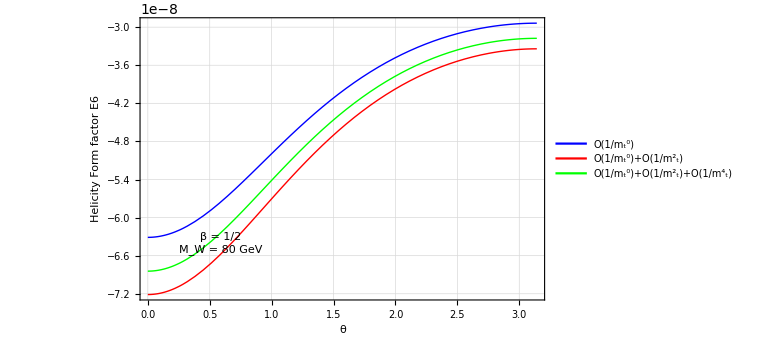

```mathematica
pLL[6]
```

```mathematica
Clear[m32,m42,mW,β,mt]
```

### Test against exact calculation done for m_t= 500 GeV

```mathematica
Clear[mt]
```

Check stability of the expanded amplitude for m_t= 500 GeV

```mathematica
pl00m=ImporTLL["AMFlow_results_large_mt/amflow_solution_PL00M.m"] ;
pl00mx12=ImporTLL["AMFlow_results_large_mt/amflow_solution_PL00Mx12.m"]; 
pl0m0=ImporTLL["AMFlow_results_large_mt/amflow_solution_PL0M0.m"] ;
pl0m0x12=ImporTLL["AMFlow_results_large_mt/amflow_solution_PL0M0x12.m"] ;
npl0m=ImporTLL["AMFlow_results_large_mt/amflow_solution_NPL0M.m"] ;
npl0mx12=ImporTLL["AMFlow_results_large_mt/amflow_solution_NPL0Mx12.m"] ;
integrals=Join[pl00m,pl00mx12,pl0m0,pl0m0x12,npl0m,npl0mx12];
```

```mathematica
(*We check stability of the convergence of the series at the level of helicity form factors*)
```

```mathematica
testvlues={β->1/2,θ->ArcCos[-1/5],mW->80,m32->mW^2,m42->mW^2,mW->80,NfV2->1};
```

```mathematica
Ratiomtm2[n_]:=(EWWLLmtm2[n]//.testvlues//.{mt->500,vq->ⅈ/2,aq->-ⅈ/2,d->4})/Series[HeWWLL[n]//.JoinTLL[estvlues,integrals,{mt->500,vq->ⅈ/2,aq->-ⅈ/2,NhV2->1}],{eps,0,0}]/.NfV2->1
Ratiomtm4[n_]:=(EWWLLmtm4[n]+EWWLLmtm4[n+9]//.testvlues//.{mt->500,vq->ⅈ/2,aq->-ⅈ/2,d->4})/Series[HeWWLL[n]//.JoinTLL[estvlues,integrals,{mt->500,vq->ⅈ/2,aq->-ⅈ/2,NhV2->1}],{eps,0,0}]/.NfV2->1
```

```mathematica
SetPrecision [Series[Ratiomtm4[1],{eps,0,0}],10]
```

(0.2724436092-0.0053652433 ⅈ)+O(eps^1)

```mathematica
N@(EWWLLmtm4[2]+EWWLLmtm4[11])//.testvlues//.{d->4}/.NfV2->1
```

(0.000284831 aq^2+0.000284831 vq^2)/mt^4+(0.0000364101 aq vq)/mt^4

```mathematica
test=N[ -4/3*1/(m32^2+S U-2U m32+U^2)//.testvlues]
```

1.90735×10^-8

```mathematica
Num[x_]=x;
Den[x_]=1/x;
```

Left-Left configuration

```mathematica
AWWLLm0= N[CLL(EWWLLm0[1]*Spba[2,3,1]Spba[6,1,5]Spba[8,1,7]+EWWLLm0[2]*Spba[2,3,1]Spba[6,2,5]Spba[8,1,7]+EWWLLm0[3]*Spba[2,3,1]Spba[6,1,5]Spba[8,2,7]+EWWLLm0[4]*Spba[2,3,1]Spba[6,2,5]Spba[8,2,7]-EWWLLm0[5]*Spba[2,3,1]Spaa[5,7]Spbb[8,6]+EWWLLm0[6]*Spba[6,1,5]Spaa[1,7]Spbb[8,2]+EWWLLm0[7]*Spba[6,2,5]Spaa[1,7]Spbb[8,2]+EWWLLm0[8]*Spba[8,1,7]Spaa[1,5]Spbb[6,2]+EWWLLm0[9]*Spba[8,2,7]Spaa[1,5]Spbb[6,2])];
```

```mathematica
AWWLLmtm2= N[CLL(EWWLLmtm2[1]*Spba[2,3,1]Spba[6,1,5]Spba[8,1,7]+EWWLLmtm2[2]*Spba[2,3,1]Spba[6,2,5]Spba[8,1,7]+EWWLLmtm2[3]*Spba[2,3,1]Spba[6,1,5]Spba[8,2,7]+EWWLLmtm2[4]*Spba[2,3,1]Spba[6,2,5]Spba[8,2,7]-EWWLLmtm2[5]*Spba[2,3,1]Spaa[5,7]Spbb[8,6]+EWWLLmtm2[6]*Spba[6,1,5]Spaa[1,7]Spbb[8,2]+EWWLLmtm2[7]*Spba[6,2,5]Spaa[1,7]Spbb[8,2]+EWWLLmtm2[8]*Spba[8,1,7]Spaa[1,5]Spbb[6,2]+EWWLLmtm2[9]*Spba[8,2,7]Spaa[1,5]Spbb[6,2])];
```

```mathematica
AWWLLmtm4= N[CLL((EWWLLmtm4[1]+EWWLLmtm4[10])*Spba[2,3,1]Spba[6,1,5]Spba[8,1,7]+(EWWLLmtm4[2]+EWWLLmtm4[11])*Spba[2,3,1]Spba[6,2,5]Spba[8,1,7]+(EWWLLmtm4[3]+EWWLLmtm4[12])*Spba[2,3,1]Spba[6,1,5]Spba[8,2,7]+(EWWLLmtm4[4]+EWWLLmtm4[13])*Spba[2,3,1]Spba[6,2,5]Spba[8,2,7]-(EWWLLmtm4[5]+EWWLLmtm4[14])*Spba[2,3,1]Spaa[5,7]Spbb[8,6]+(EWWLLmtm4[6]+EWWLLmtm4[15])*Spba[6,1,5]Spaa[1,7]Spbb[8,2]+(EWWLLmtm4[7]+EWWLLmtm4[16])*Spba[6,2,5]Spaa[1,7]Spbb[8,2]+(EWWLLmtm4[8]+EWWLLmtm4[17])*Spba[8,1,7]Spaa[1,5]Spbb[6,2]+(EWWLLmtm4[9]+EWWLLmtm4[18])*Spba[8,2,7]Spaa[1,5]Spbb[6,2])];
```

```mathematica
SetPrecision[(2*AWWLLm0)//.testvlues,10]
SetPrecision[(2*AWWLLm0+AWWLLmtm2)//.testvlues,10]
SetPrecision[(2*AWWLLm0+AWWLLmtm4)//.testvlues,10]
```

303798.4419+72601.5735 ⅈ

303275.7164+72744.3913 ⅈ

303047.9952+72502.9437 ⅈ

```mathematica
Re[(2*AWWLLm0+AWWLLmtm2)//.testvlues]/Im[(2*AWWLLm0+AWWLLmtm2)//.testvlues]
```

2.87894

```mathematica
1071.827685027612/Re[(2*AWWLLm0+AWWLLmtm2)//.testvlues]
```

0.0443629

0.707107

```mathematica
1071.827685027612/395.318437150354
```

2.7113

```mathematica
(*second phase space point*)
```

```mathematica
(*p1={183.5325871,0,0,183.5325871};
p2={183.5325871,0,0,−183.5325871};
p5=-{155.3270581,79.16327619,−19.94432084,132.1434627};
p6=-{28.20552903,19.94432084,19.94432084,0};
p7=-{174.3120610,−105.6274936,0,−138.6633593};
p8=-{9.220526124,6.519896548,0,6.519896548};*)
```

```mathematica
(*S=MP[p1+p2,p1+p2];
T=MP[p1+p3,p1+p3];
U=MP[p2+p3,p2+p3];*)
```

```mathematica
(*CLL= Spba[1,3,2] Spaa[1,2]/Spbb[1,2];
CLR= Spab[1,3,2];*)
```

```mathematica
(*AWWLLm0= N[CLL(EWWLLm0[1]*Spba[2,3,1]Spba[6,1,5]Spba[8,1,7]+EWWLLm0[2]*Spba[2,3,1]Spba[6,2,5]Spba[8,1,7]+EWWLLm0[3]*Spba[2,3,1]Spba[6,1,5]Spba[8,2,7]+EWWLLm0[4]*Spba[2,3,1]Spba[6,2,5]Spba[8,2,7]-EWWLLm0[5]*Spba[2,3,1]Spaa[5,7]Spbb[8,6]+EWWLLm0[6]*Spba[6,1,5]Spaa[1,7]Spbb[8,2]+EWWLLm0[7]*Spba[6,2,5]Spaa[1,7]Spbb[8,2]+EWWLLm0[8]*Spba[8,1,7]Spaa[1,5]Spbb[6,2]+EWWLLm0[9]*Spba[8,2,7]Spaa[1,5]Spbb[6,2])];*)
```

```mathematica
(*AWWLLmtm2= N[CLL(EWWLLmtm2[1]*Spba[2,3,1]Spba[6,1,5]Spba[8,1,7]+EWWLLmtm2[2]*Spba[2,3,1]Spba[6,2,5]Spba[8,1,7]+EWWLLmtm2[3]*Spba[2,3,1]Spba[6,1,5]Spba[8,2,7]+EWWLLmtm2[4]*Spba[2,3,1]Spba[6,2,5]Spba[8,2,7]-EWWLLmtm2[5]*Spba[2,3,1]Spaa[5,7]Spbb[8,6]+EWWLLmtm2[6]*Spba[6,1,5]Spaa[1,7]Spbb[8,2]+EWWLLmtm2[7]*Spba[6,2,5]Spaa[1,7]Spbb[8,2]+EWWLLmtm2[8]*Spba[8,1,7]Spaa[1,5]Spbb[6,2]+EWWLLmtm2[9]*Spba[8,2,7]Spaa[1,5]Spbb[6,2])];*)
```

```mathematica
(*AWWLLmtm4= N[CLL((EWWLLmtm4[1]+EWWLLmtm4[10])*Spba[2,3,1]Spba[6,1,5]Spba[8,1,7]+(EWWLLmtm4[2]+EWWLLmtm4[11])*Spba[2,3,1]Spba[6,2,5]Spba[8,1,7]+(EWWLLmtm4[3]+EWWLLmtm4[12])*Spba[2,3,1]Spba[6,1,5]Spba[8,2,7]+(EWWLLmtm4[4]+EWWLLmtm4[13])*Spba[2,3,1]Spba[6,2,5]Spba[8,2,7]-(EWWLLmtm4[5]+EWWLLmtm4[14])*Spba[2,3,1]Spaa[5,7]Spbb[8,6]+(EWWLLmtm4[6]+EWWLLmtm4[15])*Spba[6,1,5]Spaa[1,7]Spbb[8,2]+(EWWLLmtm4[7]+EWWLLmtm4[16])*Spba[6,2,5]Spaa[1,7]Spbb[8,2]+(EWWLLmtm4[8]+EWWLLmtm4[17])*Spba[8,1,7]Spaa[1,5]Spbb[6,2]+(EWWLLmtm4[9]+EWWLLmtm4[18])*Spba[8,2,7]Spaa[1,5]Spbb[6,2])];*)
```

```mathematica
(*(2*AWWLLm0+AWWLLmtm2)//.testvlues
(2*AWWLLm0+AWWLLmtm4)//.testvlues*)
```

-10375.1+3125.36 ⅈ

-18915.7-14795.6 ⅈ

```mathematica
(*Re[(2*AWWLLm0+AWWLLmtm2)//.testvlues]/Im[(2*AWWLLm0+AWWLLmtm2)//.testvlues]
Re[(2*AWWLLm0+AWWLLmtm4)//.testvlues]/Im[(2*AWWLLm0+AWWLLmtm4)//.testvlues]*)
```

```mathematica
(*7791.28734007197/9509.73549766894*)
```

0.819296

Left-Right configuration

```mathematica
AWWLRm0= N[CLR(EWWLRm0[1]*Spba[2,3,1]Spba[6,1,5]Spba[8,1,7]+EWWLRm0[2]*Spba[2,3,1]Spba[6,2,5]Spba[8,1,7]+EWWLRm0[3]*Spba[2,3,1]Spba[6,1,5]Spba[8,2,7]+EWWLRm0[4]*Spba[2,3,1]Spba[6,2,5]Spba[8,2,7]-EWWLRm0[5]*Spba[2,3,1]Spaa[5,7]Spbb[8,6]+EWWLRm0[6]*Spba[6,1,5]Spaa[1,7]Spbb[8,2]+EWWLRm0[7]*Spba[6,2,5]Spaa[1,7]Spbb[8,2]+EWWLRm0[8]*Spba[8,1,7]Spaa[1,5]Spbb[6,2]+EWWLRm0[9]*Spba[8,2,7]Spaa[1,5]Spbb[6,2])];
```

```mathematica
AVWWLR= N[CLR(EVWWLR[1]*Spba[2,3,1]Spba[6,1,5]Spba[8,1,7]+EVWWLR[2]*Spba[2,3,1]Spba[6,2,5]Spba[8,1,7]+EVWWLR[3]*Spba[2,3,1]Spba[6,1,5]Spba[8,2,7]+EVWWLR[4]*Spba[2,3,1]Spba[6,2,5]Spba[8,2,7]-EVWWLR[5]*Spba[2,3,1]Spaa[5,7]Spbb[8,6]+EVWWLR[6]*Spba[6,1,5]Spaa[1,7]Spbb[8,2]+EVWWLR[7]*Spba[6,2,5]Spaa[1,7]Spbb[8,2]+EVWWLR[8]*Spba[8,1,7]Spaa[1,5]Spbb[6,2]+EVWWLR[9]*Spba[8,2,7]Spaa[1,5]Spbb[6,2])];
```

```mathematica
AWWLRm0
```

70219.8-37246.2 ⅈ

```mathematica
AVWWLR
```

-5246.78+25283.1 ⅈ

```mathematica
αs[2mW]/(2π)(AVWWLR+AWWLRm0)/.testvlues
```

1104.94-203.444 ⅈ